```mathematica
Import["TwoAxisDateListPlot.m"]
```

```mathematica
SetDirectory["/Users/padamson/Mathematica/indicators"]
```

/Users/padamson/Mathematica/indicators

```mathematica
monthlybegindate=DatePlus[{-3,"Year"}];
weeklybegindate=DatePlus[{-1,"Year"}];
enddate=DatePlus[0];
```

```mathematica
Import["FRED.m"]
```

```mathematica
SetOptions[TwoAxisDateListPlot,"ImageSize"->400];
```

```mathematica
SetOptions[FREDm,"api_key"->"22ede6e3945e6e05a4042e6cc3e53d9d"];
```

```mathematica
SetOptions[FREDw,"api_key"->"22ede6e3945e6e05a4042e6cc3e53d9d"];
```

LeftPlot[data_, name_, title_, text_, plotrange_: All] := DateListPlot[
   data,
    Joined -> True, 
       PlotStyle -> Blue, ImagePadding -> 75, Frame -> {True, True, True, False}, 
       FrameStyle -> {Automatic, Blue, Automatic, Automatic}, 
       FrameLabel -> {"Date", name, title}, PlotRange -> plotrange, ImageSize -> 600,
       Prolog -> {
     Text[
      Style[text, Medium, Bold, Red],
      {
       data[[(Length[data] - Mod[Length[data], 2])/2, 1]],
       Min[data[[All, 2]]] + 0.9*(Max[data[[All, 2]]] - Min[data[[All, 2]]])
       },
       Center]}
   ]; 
RightPlot[data_, name_, plotrange_: All] := DateListPlot[
   data,
   Joined -> True, 
   PlotStyle -> Red, 
       ImagePadding -> 75, ImageSize -> 600, Axes -> False, Frame -> {False, False, False, True}, 
       FrameTicks -> {None, None, None, All}, FrameStyle -> 
         {Automatic, Automatic, Automatic, Red}, 
       FrameLabel -> {"", "", "", name},
   PlotRange -> plotrange];

# 6 Key Stock Market Indicators to Watch

http://www.kiplinger.com/slideshow/investing/T052-S001-6-key-stock-market-indicators-to-watch-slide-show/index.html#VEQZcU4oQ5l0MEIz.99

## S&P 500 200-Day Moving Average

WHAT IT IS: The average of daily closing prices of Standard & Poor’s 500-stock index over a period of time.

WHY IT MATTERS: Many analysts draw the dividing line between bear and bull markets by looking at the moving average. If the S&P 500 is trading above its moving average, the thinking goes, it’s a bull market -- time to invest. If it moves below the average, it’s a bear market.

```mathematica
maplot=TradingChart[{"SP500",weeklybegindate},{"Volume",{"SimpleMovingAverage",200}},ImageSize->400]
filedate = DateString[{"Hour24", "Minute", ".", "Second", "-", "MonthShort", "-", "Day", "-", "Year"}];
filename = StringJoin[Directory[],"/plots/ma-", filedate, ".eps"];
Export[filename, maplot]
```

-Graphics-

/Users/padamson/Mathematica/indicators/plots/ma-2149.17-12-16-2014.eps

## Consumer Confidence Index

WHAT IT IS: A monthly gauge of how consumers feel about the economy and their personal finances. 

WHY IT MATTERS: Consumer spending accounts for 70% of the country’s gross domestic product. When consumers are worried about the future, they spend less. When they’re optimistic, they spend more. A rise in spending could help revive the economy and lift the stock market.

```mathematica
ParentDirectory[]
```

/Users/padamson/Mathematica

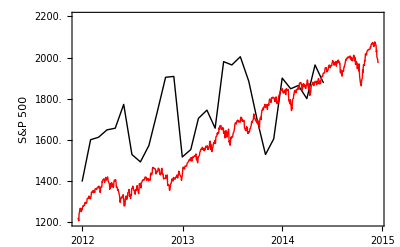

/Users/padamson/Mathematica/indicators/plots/cci-2149.19-12-16-2014.eps

```mathematica
consumerdata=FREDm["UMCSENT",monthlybegindate,enddate,"file_type"->"xml"];
sandpdata=FinancialData["SP500",monthlybegindate];
cciplot=TwoAxisDateListPlot[consumerdata,sandpdata,
FrameLabel->{"",Style["S&P 500",Red,Bold],"",Style["Consumer Confidence Index",Black,Bold]},
PlotStyle->{{Thick,Black},{Thick,Red}}
]
filedate = DateString[{"Hour24", "Minute", ".", "Second", "-", "MonthShort", "-", "Day", "-", "Year"}];
filename = StringJoin[Directory[],"/plots/cci-", filedate, ".eps"];
Export[filename, cciplot]
(*Export[filename, Overlay[{etfplot, cbotplot}, ImageSize -> 500]]*)

(*consumerplot=LeftPlot[consumerdata,"Consumer Confidence Index","S&P 500 and Monthly Consumer Confidence Index","Higher CCI could mean more spending and rising stock prices."];
sandpplot=RightPlot[sandpdata,"S&P 500"];
Overlay[{consumerplot,sandpplot}]*)
```

## Weekly Unemployment Insurance Claims

WHAT IT IS: The number of initial claims for unemployment benefits nationwide, reported weekly by the U.S. Department of Labor. 

WHY IT MATTERS: Basically, the higher the number, the weaker the economy. When claims decline it’s an early indication that the pace of layoffs is slowing, which is a good sign that executives are becoming more confident.

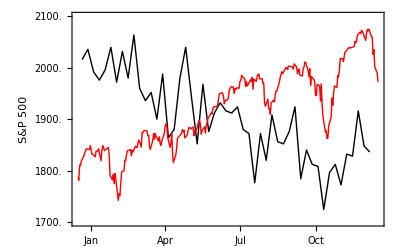

/Users/padamson/Mathematica/indicators/plots/ui-2149.20-12-16-2014.eps

```mathematica
uidata=FREDw["ICSA",weeklybegindate,enddate,"file_type"->"xml"];
sandpdata=FinancialData["SP500",weeklybegindate];
uiplot=TwoAxisDateListPlot[uidata,sandpdata,
FrameLabel->{"",Style["S&P 500",Red,Bold],"",Style["Weekly Unemployment Insurance Claims",Black,Bold]},
PlotStyle->{{Thick,Black},{Thick,Red}}
]
filedate = DateString[{"Hour24", "Minute", ".", "Second", "-", "MonthShort", "-", "Day", "-", "Year"}];
filename = StringJoin[Directory[],"/plots/ui-", filedate, ".eps"];
  (*Export[filename, Overlay[{etfplot, cbotplot}, ImageSize -> 500]]*)
  Export[filename, uiplot]
(*uiplot=LeftPlot[uidata,"Unemployment Insurance Claims","S&P 500 and Weekly Unemployment Insurance Claims","The higher the number, the weaker the economy."];
sandpplot=RightPlot[sandpdata,"S&P 500"];
Overlay[{uiplot,sandpplot}]*)
```

## U.S. Dollar

WHAT IT IS: The dollar is the world’s premier currency, and its strength or weakness has an impact on our economy and the stock market. 

WHY IT MATTERS: In recent years when the dollar has strengthened -- as measured against a basket of other key currencies, including the yen, the euro and the British pound -- the U.S. stock market has dropped. And when the dollar has been weak, the S&P 500 has risen.

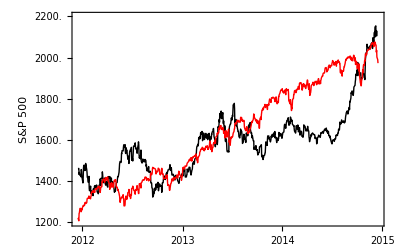

/Users/padamson/Mathematica/indicators/plots/dollar-2149.21-12-16-2014.eps

```mathematica
dollardata=FREDw["DTWEXM",monthlybegindate,enddate,"file_type"->"xls"];
dollardata=DeleteCases[dollardata,{_,y_}/;y<0.001];
sandpdata=FinancialData["SP500",monthlybegindate];
dollarplot=TwoAxisDateListPlot[dollardata,sandpdata,
FrameLabel->{"",Style["S&P 500",Red,Bold],"",Style["Trade Weighted USD Index",Black,Bold]},
PlotStyle->{{Thick,Black},{Thick,Red}}
]
filedate = DateString[{"Hour24", "Minute", ".", "Second", "-", "MonthShort", "-", "Day", "-", "Year"}];
filename = StringJoin[Directory[],"/plots/dollar-", filedate, ".eps"];
  (*Export[filename, Overlay[{etfplot, cbotplot}, ImageSize -> 500]]*)
  Export[filename, dollarplot]
(*dollarplot=LeftPlot[dollardata,"Trade Weighted USD Index","S&P 500 and Trade Weighted USD Index","A strong USD indicates a drop in S&P 500"];
Overlay[{dollarplot,sandpplot}]*)
```

## Emerging Markets

WHAT IT IS: Stock markets in developing nations. 

WHY IT MATTERS: As you can see from the chart, the stocks of emerging markets and U.S. stocks move roughly in tandem. However, the growth of the consumer class in emerging markets has fueled sales for many U.S. companies, so strength in the stock markets of countries such as Brazil, China and India bodes well for the stocks of companies in developed markets.

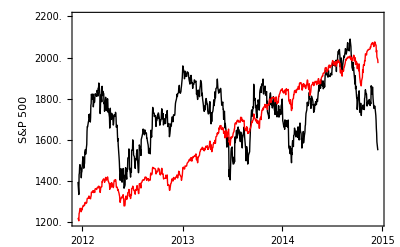

/Users/padamson/Mathematica/indicators/plots/eem-2149.22-12-16-2014.eps

```mathematica
emergingdata=FinancialData["EEM",monthlybegindate];
sandpdata=FinancialData["SP500",monthlybegindate];
eemplot=TwoAxisDateListPlot[emergingdata,sandpdata,
FrameLabel->{"",Style["S&P 500",Red,Bold],"",Style["Emerging Markets ETF (EEM)",Black,Bold]},
PlotStyle->{{Thick,Black},{Thick,Red}}
]
filedate = DateString[{"Hour24", "Minute", ".", "Second", "-", "MonthShort", "-", "Day", "-", "Year"}];
filename = StringJoin[Directory[],"/plots/eem-", filedate, ".eps"];
  (*Export[filename, Overlay[{etfplot, cbotplot}, ImageSize -> 500]]*)
  Export[filename, eemplot]
(*emergingplot=LeftPlot[emergingdata,"Emerging Markets ETF (EEM)","S&P 500 and Emerging Markets ETF","The stocks of emerging markets and U.S. stocks move roughly in tandem."];
Overlay[{emergingplot,sandpplot}]*)
```

## Price-to-Earnings Ratio of S&P 500 Over Time

WHAT IT IS: The price of the index divided by the sum of the operating earnings per share of the companies in the index. 

WHY IT MATTERS: Earnings relative to the price of the S&P 500 offer a look at how investors view the prospects for corporate profits. A falling P/E could mean investors are losing confidence in the earnings outlook and the overall economy; a rising P/E means they’re bullish.

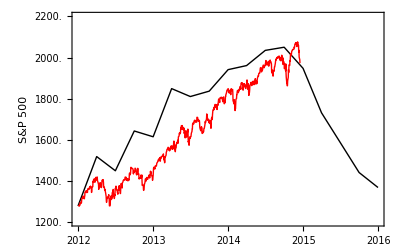

/Users/padamson/Mathematica/indicators/plots/pe-2149.24-12-16-2014.eps

```mathematica
pedata=Import["http://www.spindices.com/documents/additional-material/sp-500-eps-est.xlsx"][[1]];
(*Inlude estimated data:*)
pedata=Join[pedata[[74;;79]][[All,{1,8}]],pedata[[82;;92]][[All,{1,8}]]];
(*Do not include estimated data: pedata=pedata[[82;;115]][[All,{1,8}]];*)
pedata[[6]]={StringSplit[pedata[[6]][[1]]][[1]],pedata[[6,2]]};
pedata=DeleteCases[pedata,{_,y_}/;y>20];
sandpdata=FinancialData["SP500",pedata[[Length[pedata],1]]];
peplot=TwoAxisDateListPlot[pedata,sandpdata,
FrameLabel->{"",Style["S&P 500",Red,Bold],"",Style["P/E Ratio of S&P 500",Black,Bold]},
PlotStyle->{{Thick,Black},{Thick,Red}}]
filedate = DateString[{"Hour24", "Minute", ".", "Second", "-", "MonthShort", "-", "Day", "-", "Year"}];
filename = StringJoin[Directory[],"/plots/pe-", filedate, ".eps"];
  (*Export[filename, Overlay[{etfplot, cbotplot}, ImageSize -> 500]]*)
  Export[filename, peplot]
(*peplot=RightPlot[pedata,"S&P 500 P/E Ratio",{12,20}];
sandpplot=LeftPlot[sandpdata,"S&P 500","S&P 500 and S&P 500 P/E Ratio","A rising P/E is bullish.",{500,2100}];
Overlay[{peplot,sandpplot}]*)
```